## Exercise 1

(X_1×Y_1)\(X_2×Y_2) = (X_1×(Y_1\Y_2)) ∪ ((X_1\X_2)×Y_1)

Useful formulas:

z∈A×B⧦(∃a∈A)(∃b∈B)(z = (a,b))

(a,b)∉A×B ⧦ a∉A ∨ b∉ B

a∧(b∨c)=(a∧b)∨(a∧c)

Picture

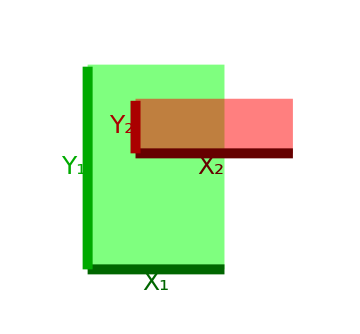
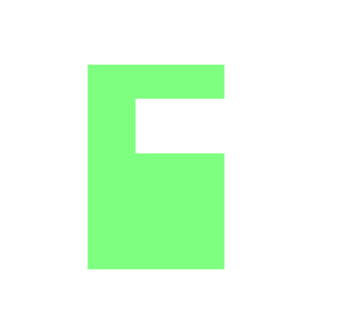
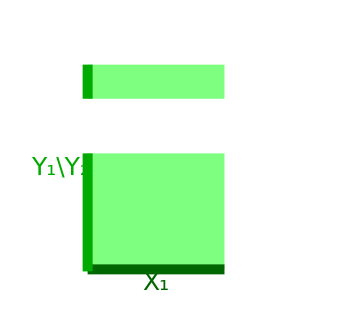
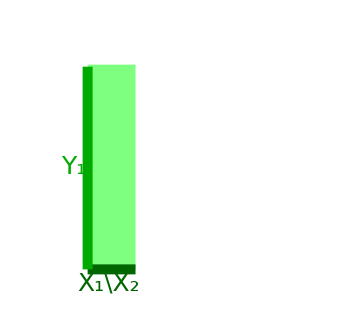
X and X | TraditionalForm` | X | TraditionalForm`
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
gr1=Graphics[{
{Green,Opacity[.5],Rectangle[{0,0},{2,3}]},
{Red,Opacity[.5],Rectangle[{.7,1.7},{3,2.5}]},
{Darker[Green,0.6],Thickness[.02],CapForm["Butt"],Line[{{0,0},{2,0}}]},
{Darker[Green],Thickness[.02],CapForm[{"Square","Butt"}],Line[{{0,0},{0,2.97}}]},
{Darker[Red,0.6],Thickness[.02],CapForm["Butt"],Line[{{.7,1.7},{3,1.7}}]},
{Darker[Red],Thickness[.02],CapForm["Square"],Line[{{.7,1.7},{.7,2.47}}]},
Text[Style["X_1",25,Darker[Green,0.6]],{1,-.2}],
Text[Style["Y_1",25,Darker[Green]],{-.2,1.5}],
Text[Style["X_2",25,Darker[Red,0.6]],{1.8,1.5}],
Text[Style["Y_2",25,Darker[Red]],{.5,2.1}]
},PlotRange->{{-0.8,3.5},{-0.5,3.5}}];
gr2=Graphics[{
{Green,Opacity[.5],Rectangle[{0,0},{2,3}]},
{White,Rectangle[{.7,1.7},{3,2.5}]}
},PlotRange->{{-0.8,3.5},{-0.5,3.5}}];
gr3=Graphics[{
{Green,Opacity[.5],Rectangle[{0,0},{2,1.7}],Rectangle[{0,2.5},{2,3}]},
{Darker[Green,0.6],Thickness[.02],CapForm["Butt"],Line[{{0,0},{2,0}}]},
{Darker[Green],Thickness[.02],CapForm["Butt"],Line[{{{0,-.03},{0,1.7}},{{0,2.5},{0,3}}}]},
Text[Style["X_1",25,Darker[Green,0.6]],{1,-.2}],
Text[Style["Y_1\Y_2",25,Darker[Green]],{-.4,1.5}]
},PlotRange->{{-0.8,3.5},{-0.5,3.5}}];
gr4=Graphics[{
{Green,Opacity[.5],Rectangle[{0,0},{.7,3}]},
{Darker[Green,0.6],Thickness[.02],CapForm["Butt"],Line[{{0,0},{.7,0}}]},
{Darker[Green],Thickness[.02],CapForm[{"Square","Butt"}],Line[{{0,0},{0,2.97}}]},
Text[Style["X_1\X_2",25,Darker[Green,0.6]],{.3,-.2}],
Text[Style["Y_1",25,Darker[Green]],{-.2,1.5}]
},PlotRange->{{-0.8,3.5},{-0.5,3.5}}];
pic=Grid[{Style[#,20]&/@{"X and X","TraditionalForm`","X","TraditionalForm`"},Show[#,ImageSize->Medium]&/@{gr1,gr2,gr3,gr4}},Frame->All]
```

## Exercise 2

f: M→N
M_1,M_2⊂ M
N_1,N_2⊂ N

Case 1

f(M_1∪M_2)=f(M_1)∪f(M_2)

Case 2

f^-1(N_1∪N_2)=f^-1(N_1)∪f^-1(N_2)

## Exercise 3

f: P(M∪N)→P(M)×P(N)

A ↦(A ∩ M, A ∩ N)

Useful formulas:

S∈P(M)⧦S⊂ M

Picture

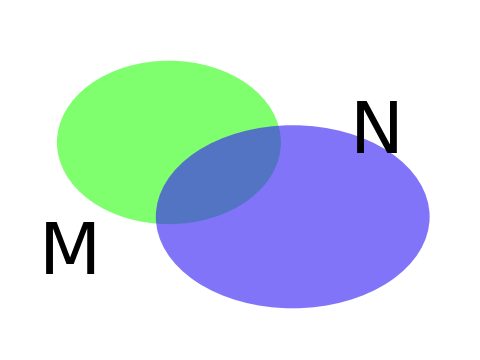
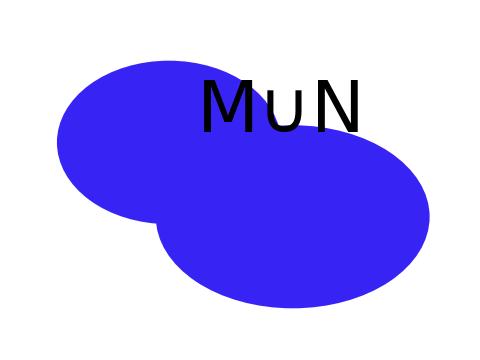
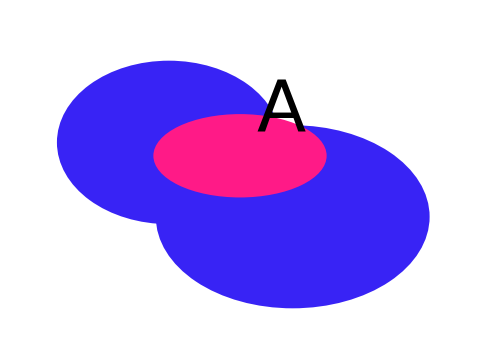
```mathematica
im1=-Graphics-;
im2=-Graphics-;
im3=-Graphics-;
im4a=-Graphics-;
im4b=-Graphics-;
Grid[{Style[#,50]&/@{"StyleBox[\"M\",FontSlant->\"Italic\"] and StyleBox[\"N\",FontSlant->\"Italic\"]","Cell[TextData[{\nStyleBox[\"M\",FontSlant->\"Italic\"],\n\" ∪ \",\nStyleBox[\"N\",FontSlant->\"Italic\"]\n}]]","Cell[TextData[{\nStyleBox[\"A \",FontSlant->\"Italic\"],\n\"⊂\",\nStyleBox[\" M\",FontSlant->\"Italic\"],\n\" ∪ \",\nStyleBox[\"N\",FontSlant->\"Italic\"]\n}]]"},Show[#,PlotStyle->{BaseStyle->FontSize->100}]&/@{im1,im2,im3}},Frame->All]
```

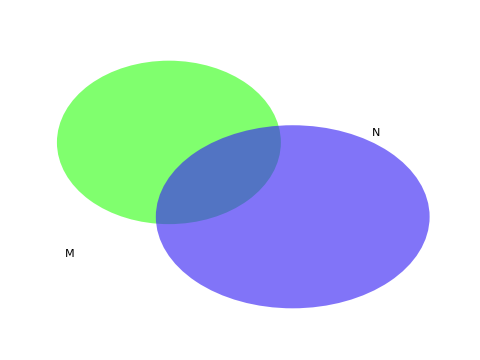
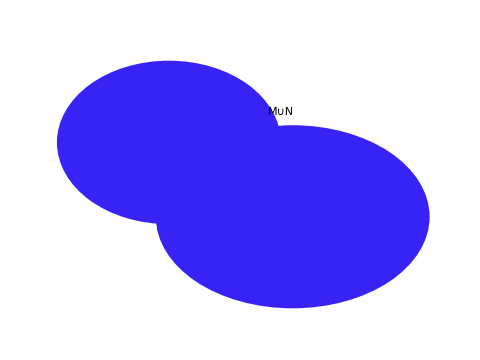
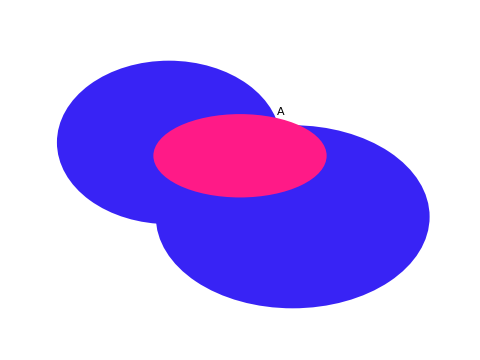
M and N | M ∪ N | A ⊂ M ∪ N
-Graphics- | -Graphics- | -Graphics-

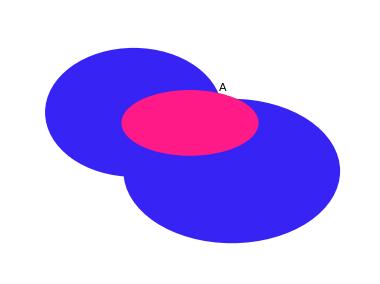
A ↦ (A ∩ M, A ∩ N) |  | 
-Graphics-↦(-Graphics-,-Graphics-) |  |

```mathematica
Grid[{{Style["A ↦ (A ∩ M, A ∩ N)",50],SpanFromLeft,SpanFromLeft},{Row[{Show[im3,ImageSize->380],Style["↦(",150],Show[im4a,ImageSize->380],Style[",",50],Show[im4b,ImageSize->380],Style[")",150]}],SpanFromLeft,SpanFromLeft}},Frame->All]
```